# The Photoelectric Effect Josephine Brozny

## Abstract/Introduction

The purpose of this lab is to show the photoelectric and calculate planks constant through that. The photoelectric effect is the property of electrons to escape from metal that is being hit with light. We are able to evaluate planks constant by finding the cutoff voltage and multiplying it with the charge of an electron in equation h=ek. We set up 2 units for our procedure, one which had a mercury lamp and photo tube and one which we controlled voltage and current readout. First we recorded the relationship between dark current and voltage, then “stopping” voltage and frequency, and finally the relationship between photo current and amount of incident light. With the data we recorded we were able to find planks constant which we found to be  1.3617×10^-30, close to the accepted value of 6.626 x 10^-34 (m^2kgs^-1).

## Description of Experimental Procedure

We used 2 parts to our apparatus in this experiment. One which held the mercury lamp and photo tube and was aimed at with light coming from the other unit which was labeled “Apparatus for Determining Plank’s Constant” and consisted of a box on rails. This box had an anode and cathode inside which experience a voltage difference when interacting with the electronics. There was also an ammeter and voltmeter inside the box which provided a measurement on the readout unit. We first preheated the mercury lamp for 20 minutes and covered the entrance to the photoelectric tube box and output of the mercury lamp source. We measured the “dark current” of the photoelectric tube while it was warming up by setting the aperture to B on the photoelectric tube, setting the voltage range to “in”/”2” by pushing the voltage range button, and rotating the voltage adjust knob fully counter clockwise. We then recorded the dark current by slowly rotating the voltage adjust knob back clockwise to increase the voltage.  After we took this data, we triggered the on off button of the photo-current input to “off”, and zeroed the ammeter by setting the current range to 10^-13 by adjusting the corresponding knob. We turned the on/off button to “on” again after zeroing.  After all this was done we were then ready to start taking “stopping-voltage” data by setting the front face of the photo-tube 30cm from the light source and setting voltage range to “out”/”I” as well as turning the the voltage knob fully counter-clockwise. We used the 365.0nm filter first and 8mm aperture size, but we recorded data for the 404.7nm, 435.8nm, 546.1nm, and 577.0nm wavelengths at the same aperture size as well. We took off the black caps on the photo-tube and light source and increased the voltage slowly until the current meter read zero for each wavelength. Next, we measured I-V characteristic curve of the photo-tube by setting the tube 30 cm apart from light source, setting current range to 10^-13, and “voltage range” to -2V/2V, selecting 435.8nm filter with 8mm aperture size, and starting with the lowest voltage of -2V and increasing it slowly, recording the change in photo-current after it had enough time to settle down. We took date for the whole voltage range and recorded 30 data points.  Finally, we determined the relationship between photo current and amount of incident light by keeping the voltage at a constant -1.50V and current range at 10^-13 for each wavelength of 365.0, 404.7, 435.8, 546.0, 577.0 and aperture size of 2nm, 4nm, and 8nm.  Finally we also measured the corresponding current to different distances of the photo tube to show the inverse square law, choosing an aperture size of 8nm, wavelength of 577.0nm, and voltage of -1.500.

## Results

### Part I: Results

It is important to measure dark current because it tells us the residual electric current in the component when there is no incident illumination. This relationship is visible in the “Dark Current vs Voltage” graph. When we look at the graph from the “Stopping Voltage vs Frequency” we can see the plateau shortly after a voltage of zero because at this point the number of photoelectrons is about equivalent to the number of incident photons. We also observe a sharp rise after a rather flat start because the work from frequency of illuminating light is more than the photon energy. Once this point is reached the electrons spike as they are excited away from the metal. As the area of the aperture gets larger (as calculated below) the photo-current actually decreases as a result of lowering intensity.  We can see here that photo-current and frequency actually have an inverse relationship, and would not expect the photo-current to vary too much. We can determine that a relationship does exist between distance and and photo current where current increases as it gets closer.

#### Data input

```mathematica
ListPlot[{{-3.00,0.00},{-1.00,0.00},{1.00,0.03},{3.00,0.09},{5.00,0.12},{9.00,0.18},{11.00,0.18},{13.00,0.21},{15.00,0.23},{17.00,0.25},{19.00,0.25},{19.98,0.25}}]
```

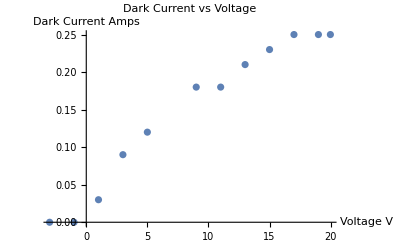

```mathematica
Show[%304,PlotLabel->HoldForm[Dark Current vs Voltage]]
```

```mathematica
data1=[{{-2.00,-90.0},{-1.7,-81},{-1.337,-27},{-1.067,457},{-1.175,140},{-1.316,-16},{-1.489,-64},{-1.740,-85},{-1.620,79},{-1.507,-68},{-1.353,-34},{-1.227,61},{-1.107,321},{-0.992,779},{-0.892,1271},{-0.787,1841},{-0.813,1675},{-0.776,1875},{0.143,8160},{0.513,11060},{1.107,17450},{1.175,18190},{1.723,24600},{1.583,22300},{1.484,21400},{1.379,19700},{1.818,26200},{1.940,27800},{1.976,27300},{1.871,26200}}]
```

```mathematica
Show[ListPlot[{data1}],ListLinePlot[{data1}]]
```

-Graphics-

didnt work like lab said

```mathematica
ListPlot[{{-2.00,-90.0},{-1.7,-81},{-1.337,-27},{-1.067,457},{-1.175,140},{-1.316,-16},{-1.489,-64},{-1.740,-85},{-1.620,79},{-1.507,-68},{-1.353,-34},{-1.227,61},{-1.107,321},{-0.992,779},{-0.892,1271},{-0.787,1841},{-0.813,1675},{-0.776,1875},{0.143,8160},{0.513,11060},{1.107,17450},{1.175,18190},{1.723,24600},{1.583,22300},{1.484,21400},{1.379,19700},{1.818,26200},{1.940,27800},{1.976,27300},{1.871,26200}}]
```

```mathematica
Show[%35,AxesLabel->{HoldForm[(Frequency Amps)/10^13],HoldForm[Voltage V]},PlotLabel->HoldForm["Stopping" Voltage vs Frequency],LabelStyle->{GrayLevel[0]}]
```

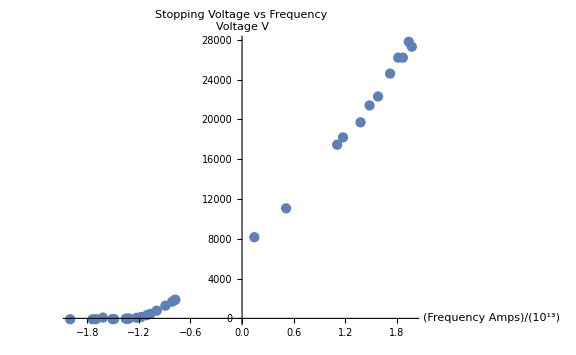

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
Show[%41,ImageSize->Large]
```

(*horizontal intersection at -85 amps*)

0.333333 a+0.333333 a x+0.333333 a x^2

```mathematica
Fit[{a},{1,x,x^2},x]
```

0.333333 a+0.333333 a x+0.333333 a x^2

```mathematica
m=Table[{{"Aperture Size","2nm","4nm","8nm"},{365.0,158,507,1485},{404.7,-3,-6,-18},{435.8,-7,-20,-76},{546.0,-8,-22,-81},{577.0,-4,-7,-26}}]
Grid[m,Frame->All]
```

{{Aperture Size,2nm,4nm,8nm},{365.,158,507,1485},{404.7,-3,-6,-18},{435.8,-7,-20,-76},{546.,-8,-22,-81},{577.,-4,-7,-26}}

Aperture Size | 2nm | 4nm | 8nm
365. | 158 | 507 | 1485
404.7 | -3 | -6 | -18
435.8 | -7 | -20 | -76
546. | -8 | -22 | -81
577. | -4 | -7 | -26

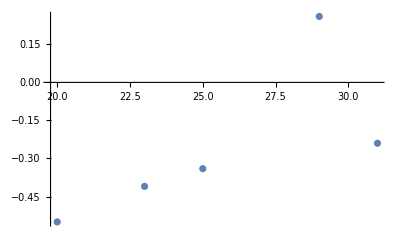

```mathematica
ListPlot[{{20,-0.55},{23,-0.41},{25,-0.34},{31,-0.24},{29,0.26}}]
```

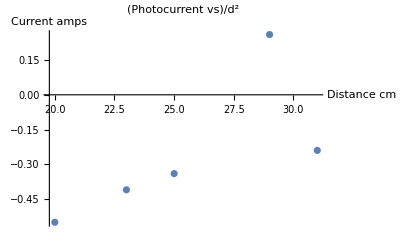

```mathematica
Show[%62,AxesLabel->{HoldForm[Distance cm],HoldForm[Current amps]},PlotLabel->HoldForm[(Photocurrent vs)/d^2],LabelStyle->{GrayLevel[0]}]
```

```mathematica
Correlation[{{20,-0.55},{23,-0.41},{25,-0.34},{31,-0.24},{29,0.26}}]
```

{{1.,0.714342},{0.714342,1.}}

#### Calculations:

```mathematica
3.14((365/2)^2)
```

104582.

```mathematica
3.14((404.7/2)^2)
```

128569.

```mathematica
3.14((435.8/2)^2)
```

149088.

```mathematica
3.14((546/2)^2)
```

234021.

```mathematica
3.14((577/2)^2)
```

261349.

Show::gtype: Times is not a type of graphics.

```mathematica
(85(10^-13))(1.602(10^-19))
```

1.3617×10^-30

## Discussion

We were able to determine the value of planks constant in this experiment which we found to be 1.3617×10^-30and is in agreement with the accepted value of 6.626 x 10^-34 (m^2kgs^-1) because of our uncertainty. We found that hoovering our hands above the apparatus tinkered with the current, therefore our bodies could have contributed to some of the uncertainty of the current. At very low current ranges such as 10^-13 the current was very unstable and was hard to read, and sometimes steadily increased or decreased after plateauing for a short amount of time which also could have contributed to the uncertainty. Lastly, the amount that we could move the voltage knob without going up or down in value could have also contributed to the uncertainty by giving that slight boost of voltage that wasn’t enough to show up on the voltage value but still affected the current that may have been on the edge of 2 values.

## Conclusion

We were able to observe the photoelectric effect throughout this experiment as we took data and calculated plank’s constant.  We took data using both units of the apparatus to see the relationships between voltage/dark current, stopping voltage/frequency, photo-current/incident light, the curve of the photo-tube, and plot-current/1d^-1 and ultimately find the cutoff voltage to calculate planks constant which we found to be 1.3617×10^-30.

## Scanned Sheets from Lab Notebook

{-Graphics-}

{-Graphics-}

{-Graphics-}